## Лабораторная работа №1

### Задание 1. Расположение точки относительно прямой

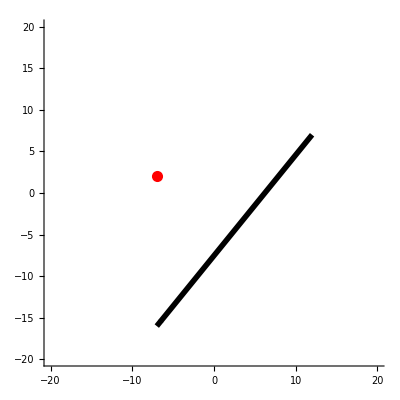

```mathematica
P[n_]:=Table[{Random[Integer,{-20,20}],Random[Integer,{-20,20}]},{n}]
P12=P[2];
P3=P[1][[1]];
Graphics[{Thickness[0.01],Arrow[P12],Red,PointSize[0.02],Point[P3]},PlotRange->{{-20,20},{-20,20}},Axes->True]
```

```mathematica
PointLocation[{P1_,P2_},P3_]:=Block[{d},d=Det[{P2-P1,P3-P1}];If[d!=0,If[d>0, Return["Точка лежит слева от прямой"],Return["Точка лежит справа от прямой"]],Return["Точка лежит на прямой"]]]
```

```mathematica
PointLocation[P12,P3]
```

Точка лежит справа от прямой

### Задание 2. Взаимное расположение прямых

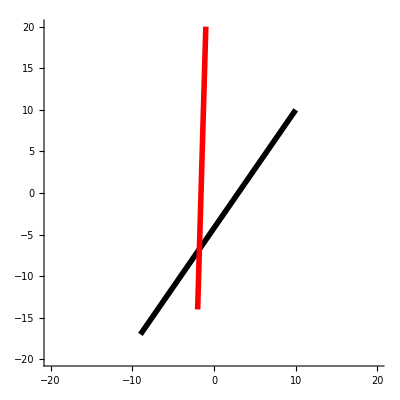

```mathematica
P[n_]:=Table[{Random[Integer,{-20,20}],Random[Integer,{-20,20}]},{n}]
P12=P[2];
P34=P[2];
Graphics[{Thickness[0.01],Line[P12],Red,Thickness[0.01],Line[P34]},PlotRange->{{-20,20},{-20,20}},Axes->True]
```

```mathematica
IntersectionCheck[{P1_,P2_},{P3_,P4_}]:=Block[{d1,d2,d3,d4},
d1=Det[{P4-P3,P1-P3}];d2=Det[{P4-P3,P2-P3}]; d3=Det[{P2-P1,P3-P1}];d4=Det[{P2-P1,P4-P1}];
scalar1=Dot[P3-P1,P4-P1];scalar2=Dot[P3-P2,P4-P2];scalar3=Dot[P3-P1,P3-P2];scalar4=Dot[P4-P1,P4-P2];
If[d1== d2== d3==d4== 0, 
If[scalar1≤0||scalar2≤ 0||scalar3≤0||scalar4≤0,Return[True],Return[False]],
If[(d1*d2<=0) && (d3*d4<=0),Return[True],Return[False]]]]
```

```mathematica
If[IntersectionCheck[P12,P34]==True,"Прямые пересекаются","Прямые не пересекаются"]
```

Прямые пересекаются

### Задание 3. Проверка многоугольника на простоту

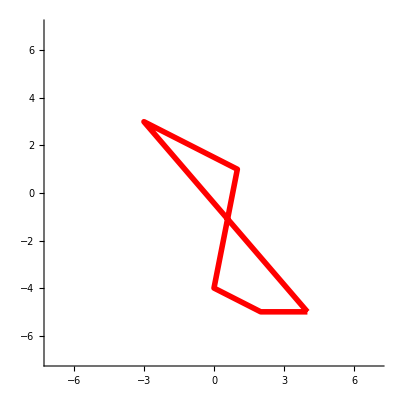

```mathematica
P[n_] := Table[{RandomInteger[{-5,5}],RandomInteger[{-5,5}]},{n}]
n = RandomInteger[{3,6}];
PolygoN = Table[P[1][[1]],{i,1,n}];
AppendTo[PolygoN,PolygoN⟦1⟧];
Graphics[{Red,Thickness[0.01],Line[PolygoN]},PlotRange->{{-7,7},{-7,7}},Axes->True]
```

```mathematica
SimplicityOfPolygoN[PolygoN_] := Block[{intersection},intersection = False;
Do[ 
If[i==1, 
Do[
intersection = IntersectionCheck[{PolygoN⟦i⟧,PolygoN⟦i+1⟧},{PolygoN⟦j⟧,PolygoN⟦j+1⟧}];
If[intersection == True,Break[]];
,{j,3,n-1}],
Do[
intersection = IntersectionCheck[{PolygoN⟦i⟧,PolygoN⟦i+1⟧},{PolygoN⟦j⟧,PolygoN⟦j+1⟧}];
If[intersection == True,Break[]];
,{j,i+2,n}]
];
If[intersection == True,Break[]]
,{i,1,n-2}
];
If[intersection == True,Return[False],Return[True]];
];
```

```mathematica
If[SimplicityOfPolygoN[PolygoN] == False, "Многоугольник не является простым","Многоугольник простой"]
```

Многоугольник не является простым

### Задание 4. Проверка многоугольника на выпуклость

```mathematica
ConvexOfPolygoN[PolygoN_] := Block[{counter,check,temp},
counter=0; 
If[SimplicityOfPolygoN[PolygoN] == False,Return["Многоугольник не является простым, поэтому и не является выпуклым"],
check=PointLocation[{PolygoN⟦1⟧,PolygoN⟦2⟧},PolygoN⟦3⟧];
Do[
If[2≤i<n,temp=PointLocation[{PolygoN⟦i⟧,PolygoN⟦i+1⟧},PolygoN⟦i+2⟧],temp=PointLocation[{PolygoN⟦i⟧,PolygoN⟦i+1⟧},PolygoN⟦2⟧]];
If[temp≠check,counter++];
,{i,2,n}
]
];
If[counter==0, Return["Многоугольник простой и выпуклый"],Return["Многоугольник простой, но не выпуклый"]]
];
ConvexOfPolygoN[PolygoN]
```

Многоугольник не является простым, поэтому и не является выпуклым